Variational Quantum Simulation of General Processes
Original authors of paper: Endo et al, PRL 125.010501 (2020)
Link to pre-print: https://link.aps.org/doi/10.1103/PhysRevLett.125.010501
Notebook by: Óscar Amaro (Apr 2024)

## Figure 3

```mathematica
(*** Ideal dynamics ***)
Clear[Id,X,Y,Z,n,ZZij,Xi,HI,J,hX,tmax,ψ0,U,t,dt,tdim,HZZij,tlst,Clst,γ]
Clear[σip,σipdg,γ,Liop,Liopdg,ρ,ρ0,Li,Lidg,ClstL,ℒρ,ℒ]

(* number of spins *)
n=6;
(* parameters as described in text *)
J=1;
hX=1;
γ=1;
tmax = 6;
tdim=1200;
dt = tmax/tdim;

(* Pauli matrices *)
{Id,X,Y,Z}=Table[PauliMatrix[i],{i,0,3}];

(* examples of Kronecker product *)
KroneckerProduct[Y,X,Z]//MatrixForm;
KroneckerProduct[Y,KroneckerProduct[X,Z]]//MatrixForm;

(* nearest-neighbors *)
ZZij[i_,j_,n_]:=Module[{k,Op},
Op={1};
For[k=1,k<=n,k++,
Op = KroneckerProduct[If[k==i ||k==j,Z,Id],Op]
];
Return[Op]
]
(* X on spin i *)
Xi[i_,n_]:=Module[{k,Op},
Op={1};
For[k=1,k<=n,k++,
Op = KroneckerProduct[If[k==i ,X,Id],Op]
];
Return[Op]
]
(*(*examples*)
ZZij[1,2,2]//MatrixForm
KroneckerProduct[Z,Z]//MatrixForm
ZZij[1,3,3]//MatrixForm
KroneckerProduct[Z,Id,Z]//MatrixForm
*)

(* Hamiltonian *)
HZZij=(ZZij[1,2,n]+ZZij[1,3,n]+ZZij[2,4,n]+ZZij[3,4,n]+ZZij[3,5,n]+ZZij[4,6,n]+ZZij[5,6,n]);
HI=J/4 HZZij+hX Sum[Xi[i,n],{i,1,n}]//N;
HI//MatrixForm;
HermitianMatrixQ[HI];

(* initial state *)
ψ0=Table[0,{i,1,2^n}];
ψ0[[1]]=1;

(* evolution operator *)
U=MatrixExp[-I HI dt];

(* initialize state *)
ψ=ψ0;
(* correlation operator *)
𝒞= HZZij/7;

(* time simulation *)
tlst=Table[t,{t,0,tmax,tmax/(tdim-1)}];
Clst=Table[0,{i,1,tdim}];
For[i=1,i<=tdim,i++,
Clst[[i]]=Conjugate[ψ].𝒞.ψ;
ψ=U.ψ;
]
```

```mathematica
(*** Lindbladian dynamics ***)
σip=KroneckerProduct[{0,1},{1,0}];
σipdg=ConjugateTranspose[σip];

(* L on spin i *)
Liop[i_,n_]:=Module[{k,Op},
Op={1};
For[k=1,k<=n,k++,
Op = KroneckerProduct[If[k==i ,Sqrt[γ] σip,Id],Op]
];
Return[Op]
]
Liopdg[i_,n_]:=Module[{k,Op},
Op={1};
For[k=1,k<=n,k++,
Op = KroneckerProduct[If[k==i ,Sqrt[γ] σipdg,Id],Op]
];
Return[Op]
]

(* initial density matrix*)
ρ0=KroneckerProduct[ψ0,ψ0];
(* list of Li operators *)
Li=Table[Liop[k,n],{k,1,n}];
Lidg=Table[Liopdg[k,n],{k,1,n}];

(* time simulation *)
ClstL=Table[0,{i,1,tdim}];
ρ=ρ0;
For[i=1,i<=tdim,i++,
ClstL[[i]]=Tr[ρ.𝒞];(* Correlation *)
ℒρ=0.5Sum[(2Li[[k]].ρ.Lidg[[k]]-Lidg[[k]].Li[[k]].ρ-ρ.Lidg[[k]].Li[[k]]),{k,1,n}];(* ℒ.ρ operator *)
ρ=ρ+dt(-I (HI.ρ-ρ.HI)+ℒρ);
]
```

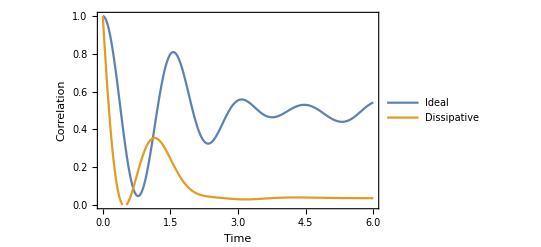

```mathematica
(* plot results *)
ListPlot[{Transpose[{tlst,Clst}],Transpose[{tlst,ClstL}]},Joined->True,PlotRange->{0,1},Frame->True,FrameLabel->{"Time","Correlation"},PlotLegends->{"Ideal","Dissipative"}]
```